### Equations

#### Root finding

```mathematica
eqPsi[x0_?NumericQ,psi_?NumericQ] := 1/psi - NIntegrate[LegendreP[2,x]^2 Exp[psi LegendreP[2,x]],{x,x0,1}]/NIntegrate[LegendreP[2,x] Exp[psi LegendreP[2,x]],{x,x0,1}] + LegendreP[2,x0]
```

```mathematica
rootx0[psi_,guess_] := x0 /. FindRoot[eqPsi[x0,psi],{x0,guess}]
```

```mathematica
rootx0find[psi_] := Module[{guess, value}, guess = 0.55 ; value= rootx0[psi, guess]; While[value > 1 || value < 0, guess = If[Sign[psi] value < 0, guess /= 2, guess = (1+guess)/2; guess]; value =  rootx0[psi, guess]];value]
```

#### Order parameters

```mathematica
S[psi_] := Module[{x0},x0=rootx0find[psi]; NIntegrate[LegendreP[2,x] (LegendreP[2,x] - LegendreP[2,x0]) Exp[psi LegendreP[2,x]],{x,x0,1}]/NIntegrate[(LegendreP[2,x] - LegendreP[2,x0]) Exp[psi LegendreP[2,x]],{x,x0,1}]]
```

```mathematica
phi[S_,psi_] := S LegendreP[2,rootx0findup[psi]]
```

#### Free energy

```mathematica
F[S_,psi_,phi_] :=psi S -Log[2 N[Pi,50] Integrate[Piecewise[{{S LegendreP[2,x] - phi,S LegendreP[2,x] - phi > 0},{0,True}}]Exp[psi LegendreP[2,x]],{x,-1,1}]]
```

### Solution

```mathematica
psiS = Table[{psi,S[psi]},{psi,Range[0.001,10,0.01]}];
```

```mathematica
psiphiS1 = Table[{tuple[[1]],phi[tuple[[2]],tuple[[1]]],tuple[[2]]},{tuple,psiS}];
```

```mathematica
psiphiS2 = Table[{0,phi,0},{phi,Range[-0.3,0,0.01]}];
```

```mathematica
Save["/Users/yketa/Research/Umeå/PT_project/code/Mathematica/psiphiS.wl",{psiS,psiphiS1,psiphiS2}]
```

### Stability

```mathematica
Do[F1=F[psiphiS1[[i]][[3]],psiphiS1[[i]][[1]],psiphiS1[[i]][[2]]];Fp1=ND[F[S,psiphiS1[[i]][[1]],psiphiS1[[i]][[2]]],S,psiphiS1[[i]][[3]]];
Fpp1=ND[F[S,psiphiS1[[i]][[1]],psiphiS1[[i]][[2]]],{S,2},psiphiS1[[i]][[3]]];{F1,Fp1,Fpp1} >>> "/Users/yketa/Research/Umeå/PT_project/code/Mathematica/FFpFpp1.wl",{i,Length[psiphiS1]}];
```

```mathematica
Run["!cat /Users/yketa/Research/Umeå/PT_project/code/Mathematica/FFpFpp1.wl | sed s,{,,g | sed s,},,g > /Users/yketa/Research/Umeå/PT_project/code/Mathematica/FFpFpp1.csv"];
```

```mathematica
FFpFpp1=Import["/Users/yketa/Research/Umeå/PT_project/code/Mathematica/FFpFpp1.csv","CSV"];
```

```mathematica
Do[F2=F[psiphiS2[[i]][[3]],psiphiS2[[i]][[1]],psiphiS2[[i]][[2]]];Fp2=ND[F[S,psiphiS2[[i]][[1]],psiphiS2[[i]][[2]]],S,psiphiS2[[i]][[3]]];
Fpp2=ND[F[S,psiphiS2[[i]][[1]],psiphiS2[[i]][[2]]],{S,2},psiphiS2[[i]][[3]]];{F2,Fp2,Fpp2} >>> "/Users/yketa/Research/Umeå/PT_project/code/Mathematica/FFpFpp2.wl",{i,Length[psiphiS2]}];
```

```mathematica
Run["!cat /Users/yketa/Research/Umeå/PT_project/code/Mathematica/FFpFpp2.wl | sed s,{,,g | sed s,},,g > /Users/yketa/Research/Umeå/PT_project/code/Mathematica/FFpFpp2.csv"];
```

```mathematica
FFpFpp2 = Import["/Users/yketa/Research/Umeå/PT_project/code/Mathematica/FFpFpp2.csv","CSV"];
```

### Plots

#### Raw plot

```mathematica
phiS1 = Table[{tuple[[2]],tuple[[3]]},{tuple,psiphiS1}];
```

```mathematica
phiS2= Table[{tuple[[2]],tuple[[3]]},{tuple,psiphiS2}];
```

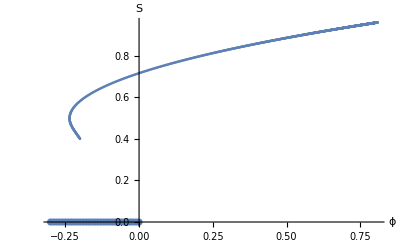

```mathematica
p01 = ListPlot[phiS1]; p02 = ListPlot[phiS2]; Show[p01,p02,PlotRange->All,AxesLabel->{Text[Style[ToExpression["\\phi",TeXForm,HoldForm],Medium]],Text[Style[ToExpression["S",TeXForm,HoldForm],Medium]]}]
```

#### Stability plot

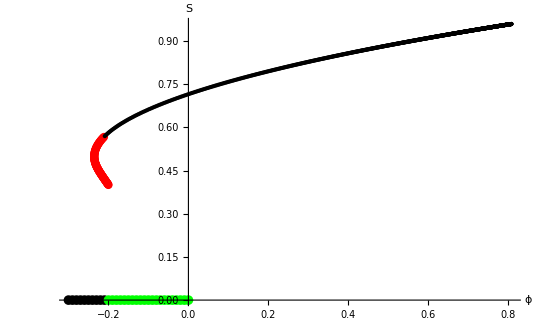

```mathematica
p1=ListPlot[phiS1[[1;;83]],PlotStyle->Red];p2=ListPlot[phiS1[[84;;Length[phiS1]]],PlotStyle->Black]; p3 = ListPlot[phiS2[[1;;10]],PlotStyle->Black]; p4 = ListPlot[phiS2[[11;;Length[phiS2]]],PlotStyle->Green]; FinalPlot=Show[p1,p2,p3,p4,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{Text[Style[ToExpression["\\phi",TeXForm,HoldForm],Medium]],Text[Style[ToExpression["S",TeXForm,HoldForm],Medium]]}]
```

```mathematica
Export["/Users/yketa/Research/Umeå/PT_project/code/Mathematica/FinalPlot.eps",FinalPlot]
```

/Users/yketa/Research/Umeå/PT_project/code/Mathematica/FinalPlot.eps